# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=1;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

ia=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
id=reduire[ColorConvert[clean@Import[pathResult],"GrayScale"],reduce];

ImageDimensions[ia];

ia;

(*{1,44},{1,102} arbitrary size to make the method faster *)
nx=3000/reduce;
ny=1000/reduce;
{ia,ib,id}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id}
ImageDimensions[#]&/@{ia,ib,id}

mag=(max-min);

max=Max[ImageData[id]]
min=Min[ImageData[id]]
```

-Graphics-

ImageTake::takec: Cannot take the specified columns of the image.

General::stop: Further output of ImageTake::takec will be suppressed during this calculation.

{ImageTake[-Graphics-,{1000,1044},{3000,3102}],ImageTake[-Graphics-,{1000,1044},{3000,3102}],ImageTake[-Graphics-,{1000,1044},{3000,3102}]}

ImageDimensions::imginv: Expecting an image or graphics instead of ImageTake[-Image-, {1000, 1044}, {3000, 3102}].

General::stop: Further output of ImageDimensions::imginv will be suppressed during this calculation.

{ImageDimensions[ImageTake[-Graphics-,{1000,1044},{3000,3102}]],ImageDimensions[ImageTake[-Graphics-,{1000,1044},{3000,3102}]],ImageDimensions[ImageTake[-Graphics-,{1000,1044},{3000,3102}]]}

ImageData::imginv: Expecting an image or graphics instead of ImageTake[-Image-, {1000, 1044}, {3000, 3102}].

ImageData[ImageTake[-Graphics-,{1000,1044},{3000,3102}]]

ImageData::imginv: Expecting an image or graphics instead of ImageTake[-Image-, {1000, 1044}, {3000, 3102}].

ImageData[ImageTake[-Graphics-,{1000,1044},{3000,3102}]]

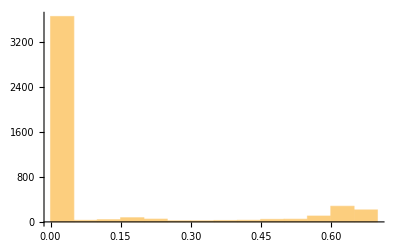

```mathematica
Histogram[Flatten[ImageData[id]]]
```

```mathematica
id/max
```

-Graphics-

```mathematica
ImageData[id/max]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.231704,0.407436,0.936912,0.87674,0.901543,0.901543,0.716709,0.784996,0.690913,0.268299,0.888582,0.888582,0.526979,0.0629181,0.309223,0.869664,0.992232,0.990649,0.987959,0.973761,0.956415,0.888066,0.927685,0.928735,0.934812,0.934812,0.233804,0.172582,0.914259,0.873103,0.697717,0.697717,0.504435,0.650279,0.956415,0.948885,0.907376,0.927282,0.953668,0.89075,0.896112,0.896112,0.278915,0.172582,0.915309,0.915309,0.791998,0.839856,0.706694,0.678475,0.636632,0.144908,0.302215,0.122687,0.0532886,0.210226,0.,0.,0.10698,0.45051,0.945089,0.885966,0.345567,0.172582,0.,0.749252,1.,0.748203,0.307526,0.,0.,0.,0.,0.,0.,0.0532886,0.831339,0.836769,0.896112,0.896112,0.278915},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.292926,0.936912,0.930431,0.926295,0.913919,0.8531,0.813941,0.685483,0.397806,0.863836,0.888582,0.278513,0.,0.,0.805049,0.931447,0.889127,0.966742,0.917386,0.967281,0.951631,0.939011,0.935862,0.947835,0.939658,0.11556,0.172582,0.856187,0.838869,0.707506,0.751255,0.610745,0.619677,0.954718,0.946138,0.842824,0.913919,0.941355,0.848379,0.888582,0.890279,0.278915,0.172582,0.855137,0.909879,0.752657,0.85217,0.796418,0.736508,0.721328,0.307458,0.0526417,0.,0.,0.,0.,0.,0.,0.295672,0.945089,0.945089,0.119941,0.,0.,0.749252,1.,0.62505,0.,0.,0.,0.,0.,0.,0.0499577,0.308042,0.831339,0.840503,0.890279,0.890682,0.278915},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.233804,0.599339,0.968853,0.95583,0.937961,0.927747,0.449863,0.761702,0.76917,0.314925,0.,0.,0.,0.0612839,0.649292,0.672057,0.605916,0.871292,0.996141,0.918498,0.958514,0.96231,0.966753,0.906582,0.12099,0.,0.54996,0.788729,0.808862,0.983941,0.983941,0.749786,0.953668,0.888066,0.871485,0.871485,0.835073,0.834023,0.876916,0.876916,0.273082,0.0553882,0.901543,0.902593,0.909476,0.909073,0.866702,0.866702,0.849423,0.85007,0.424187,0.,0.,0.,0.,0.,0.,0.,0.234854,0.119941,0.,0.,0.,0.0612839,0.250101,0.,0.,0.,0.,0.,0.,0.,0.720625,0.823871,0.831986,0.835719,0.883799,0.883799,0.386542},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.484426,0.968853,0.962373,0.959167,0.941758,0.720914,0.790307,0.765436,0.358647,0.0532886,0.,0.,0.,0.545659,0.672057,0.419261,0.74709,0.996141,0.973529,0.955535,0.968915,0.97657,0.908681,0.0601717,0.,0.710297,0.812954,0.775315,0.926573,0.98616,0.726356,0.962957,0.891862,0.911944,0.891391,0.839856,0.835073,0.872535,0.876916,0.563908,0.344115,0.916603,0.911172,0.920155,0.912625,0.814463,0.871485,0.85112,0.829705,0.363431,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.297772,0.180112,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.618428,0.827605,0.829302,0.829705,0.878368,0.883799,0.277463},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0601717,0.239699,0.87089,0.99895,0.986325,0.974811,0.946206,0.717294,0.831986,0.572204,0.,0.,0.,0.0423483,0.168099,0.,0.0629181,0.308701,0.943267,0.943267,0.992816,0.998366,0.622304,0.,0.610325,0.976508,0.890415,0.0612839,0.871361,0.993928,0.918441,0.973761,0.974811,0.974811,0.967281,0.0532886,0.206493,0.219391,0.452145,0.927282,0.934812,0.947188,0.948238,0.949287,0.886369,0.883799,0.883799,0.765617,0.79311,0.594085,0.,0.,0.,0.,0.,0.,0.,0.,0.356894,0.956415,0.895596,0.119294,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.733523,0.836769,0.812023,0.808289,0.723371,0.219794,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.748203,0.99895,0.92171,0.974811,0.912943,0.735753,0.850195,0.708192,0.174682,0.,0.,0.,0.,0.,0.,0.174971,0.883617,0.943267,0.868552,0.998366,0.621719,0.,0.610325,0.976508,0.852771,0.,0.865749,0.99171,0.922238,0.981416,0.980832,0.981944,0.914055,0.36174,0.182859,0.297772,0.470819,0.945622,0.94077,0.965182,0.950984,0.939011,0.939658,0.82508,0.882749,0.781846,0.817856,0.716063,0.225224,0.369394,0.306419,0.302567,0.0596497,0.,0.,0.,0.356894,0.946201,0.899449,0.169898,0.,0.,0.,0.,0.,0.,0.,0.,0.0629181,0.833569,0.847046,0.815757,0.820137,0.507714,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0612839,0.249051,0.0618684,0.304314,0.679848,0.990705,0.956664,0.933762,0.933762,0.174682,0.,0.,0.,0.,0.,0.,0.233974,0.233974,0.0612839,0.250101,0.,0.,0.0618684,0.304314,0.,0.0629805,0.983941,0.983941,0.927674,0.992283,0.992878,0.992294,0.975867,0.968853,0.964007,0.956415,0.985167,0.987794,0.99281,0.993979,0.792724,0.914259,0.913209,0.879015,0.879015,0.867752,0.868801,0.897162,0.948425,0.989009,0.974533,0.975061,0.54718,0.,0.,0.,0.,0.665702,0.807642,0.555975,0.,0.,0.,0.,0.,0.,0.,0.,0.871877,0.996726,0.789053,0.625896,0.836769,0.575938,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.61798,0.975923,0.902264,0.952096,0.939658,0.481743,0.123737,0.166102,0.277866,0.13306,0.226115,0.0456792,0.,0.35964,0.181809,0.166505,0.225224,0.,0.,0.,0.,0.120934,0.920961,0.983941,0.803409,0.992283,0.991182,0.992294,0.918441,0.968853,0.9605,0.949986,0.953373,0.968274,0.991176,0.993979,0.792724,0.935924,0.919752,0.894478,0.886948,0.914112,0.896408,0.901997,0.942353,0.981706,0.977802,0.97295,0.668108,0.294622,0.174682,0.165455,0.277866,0.744605,0.828473,0.722793,0.241277,0.347661,0.307532,0.183267,0.,0.293573,0.174682,0.,0.808959,0.979844,0.669572,0.625896,0.800981,0.558075,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.355844,0.949287,0.969965,0.986847,0.980304,0.975458,0.91044,0.889632,0.878289,0.718349,0.718349,0.359175,0.478934,0.960211,0.897293,0.901946,0.901946,0.279965,0.,0.,0.,0.,0.246248,0.246248,0.0629181,0.309223,0.0612839,0.246832,0.0601717,0.301046,0.939936,0.927662,0.891488,0.891488,0.286962,0.245658,0.54571,0.971015,0.902201,0.935862,0.970561,0.984985,0.915451,0.918782,0.966118,0.966118,0.911195,0.971015,0.901554,0.937961,0.876093,0.890682,0.899262,0.926635,0.955893,0.980304,0.940515,0.943267,0.983941,0.983941,0.480052,0.935862,0.87674,0.174682,0.23112,0.91216,0.91216,0.704033,0.747573,0.701349,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.355844,0.949287,0.967219,0.986847,0.980304,0.975458,0.902264,0.923611,0.896095,0.67267,0.718349,0.267816,0.420459,0.958514,0.948885,0.83909,0.868217,0.333901,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0596497,0.880286,0.927662,0.891488,0.891488,0.110356,0.,0.483842,0.971015,0.889729,0.916688,0.970561,0.976105,0.921063,0.924394,0.906468,0.966118,0.728456,0.955893,0.93429,0.944442,0.937558,0.926357,0.919815,0.952687,0.960801,0.982466,0.94443,0.955246,0.978505,0.971435,0.594618,0.927282,0.920802,0.11556,0.170886,0.921386,0.915956,0.599737,0.747573,0.701349,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.235903,0.177831,0.30811,0.183324,0.304314,0.672194,0.977558,0.972712,0.0873806,0.178739,0.,0.477884,0.957464,0.896646,0.723127,0.810326,0.555975,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.174971,0.233974,0.2217,0.166028,0.,0.,0.0618684,0.554897,0.772013,0.791186,0.180175,0.311447,0.229009,0.229009,0.241283,0.241283,0.11556,0.889632,0.914322,0.957464,0.969965,0.982001,0.992408,0.996732,0.992283,0.990121,0.917386,0.96231,0.958514,0.949287,0.886369,0.888582,0.888582,0.390923,0.233804,0.935862,0.935862,0.280028,0.185883,0.0924479,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.485942,0.977558,0.915689,0.,0.,0.,0.477884,0.957464,0.896646,0.555975,0.810326,0.505371,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.384834,0.772013,0.723002,0.,0.,0.,0.,0.,0.,0.112411,0.835941,0.914849,0.947704,0.943085,0.962424,0.992345,0.991295,0.988487,0.97114,0.963485,0.952034,0.950337,0.940708,0.936912,0.825727,0.874635,0.331154,0.497359,0.89214,0.935862,0.406386,0.173632,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0618684,0.244143,0.123737,0.,0.,0.,0.,0.236953,0.12099,0.0499577,0.254351,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0490101,0.241782,0.0963859,0.,0.,0.,0.,0.,0.,0.,0.220843,0.87106,0.913754,0.884179,0.890376,0.843771,0.977558,0.904363,0.914259,0.916359,0.932712,0.931663,0.923486,0.923486,0.802212,0.85007,0.716102,0.704294,0.717192,0.346617,0.924536,0.924536,0.231704,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.756022,0.913754,0.884179,0.884179,0.720035,0.977558,0.905997,0.916359,0.922436,0.932712,0.929966,0.920739,0.922436,0.752254,0.853804,0.812466,0.742585,0.804822,0.470354,0.924536,0.924536,0.113863,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0590028,0.23234,0.218369,0.110356,0.0618684,0.306011,0.231704,0.924536,0.925585,0.932066,0.929966,0.913209,0.909476,0.862968,0.874232,0.917006,0.940123,0.968915,0.907047,0.293573,0.113863,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.287495,0.924536,0.925585,0.929966,0.925585,0.924536,0.917006,0.890342,0.888645,0.928445,0.955314,0.977682,0.91149,0.286445,0.171935,0.,0.219028,0.13096},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.231704,0.346214,0.921386,0.932712,0.948238,0.948238,0.948238,0.948119,0.954491,0.993401,0.99895,0.791674,0.920739,0.920739,0.407192,0.704294,0.704294},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.230008,0.921386,0.932712,0.964597,0.955246,0.966231,0.950865,0.94485,0.984231,0.99895,0.786244,0.920739,0.920739,0.419687,0.740888,0.671246},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.230008,0.737399,0.995092,0.995676,0.993979,0.914645,0.936912,0.942405,0.365661,0.226677,0.916359,0.915309,0.91216,0.848674,0.568771},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.622888,0.977098,0.983641,0.973364,0.946972,0.936912,0.936912,0.114913,0.226677,0.916359,0.897236,0.905725,0.848674,0.729505},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.298419,0.939011,0.940708,0.89571,0.89571,0.513366,0.114913,0.,0.,0.649212,0.863547,0.819394,0.739095,0.999535},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.294622,0.939011,0.932531,0.840321,0.89571,0.279562,0.,0.,0.,0.538152,0.863547,0.594471,0.625635,0.999535},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.234854,0.114913,0.224174,0.224174,0.,0.,0.,0.,0.052341,0.269076,0.,0.0629181,0.311969},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.363436,0.182859,0.368929,0.123737,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.484426,0.97055,0.975458,0.982001,0.858264,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.304955,0.0499577,0.,0.,0.,0.,0.,0.,0.,0.0532886,0.309739,0.0532886,0.,0.,0.,0.,0.,0.,0.,0.,0.424255,0.958174,0.957589,0.967928,0.909391,0.0499577,0.307639,0.0499577,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.608214,0.810973,0.608214,0.,0.,0.,0.,0.,0.,0.,0.621759,0.828252,0.568471,0.,0.,0.,0.,0.,0.,0.,0.,0.0547413,0.900896,0.901946,0.91216,0.91216,0.779747,0.819088,0.56304,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.555975,0.810973,0.506018,0.,0.,0.,0.,0.,0.,0.,0.618428,0.81949,0.515182,0.,0.,0.,0.,0.,0.,0.,0.,0.166505,0.918702,0.911575,0.851988,0.905679,0.726458,0.788729,0.547861,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0499577,0.254351,0.,0.,0.,0.,0.,0.,0.,0.,0.658172,0.810326,0.555975,0.,0.,0.,0.,0.,0.,0.,0.,0.417712,0.954718,0.947188,0.895063,0.895063,0.648645,0.735481,0.689257,0.0462239,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.607567,0.810326,0.505371,0.,0.,0.,0.,0.,0.,0.,0.,0.356894,0.953668,0.88532,0.842421,0.895466,0.655062,0.766242,0.698018,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0499577,0.201062,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.356491,0.947188,0.884917,0.907376,0.907376,0.84902,0.840503,0.518916,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.356491,0.947188,0.937961,0.847204,0.901543,0.74204,0.845933,0.682918,0.259134,0.0532886,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.23655,0.173632,0.884849,0.883799,0.855501,0.854451,0.836769,0.835719,0.415022,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.112411,0.82508,0.879418,0.853804,0.854451,0.839453,0.835719,0.523296,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0543384,0.871485,0.872132,0.853804,0.854451,0.478525,0.209177,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0543384,0.823627,0.878368,0.863615,0.864018,0.374229,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0547413,0.903642,0.902593,0.889229,0.889229,0.332204,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.168202,0.84557,0.898212,0.836588,0.889632,0.278513,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0553882,0.897162,0.897162,0.897162,0.897162,0.278915,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.167152,0.841774,0.897162,0.841774,0.897162,0.278915,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.225224,0.225224,0.225224,0.225224,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

## Little Tests

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=4;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### Little Test: Test Row

```mathematica
combinePV[realPV_]:=Block[{srtDistinctPV,newPV,i,c,sum,solution},(

srtDistinctPV=Sort[DeleteDuplicates[Floor[realPV[[All,1]]]]];

newPV=SortBy[Flatten[{Floor[realPV[[All,1]]],realPV[[All,2]]},{{2},{1}}],First];

i=1;

Table[
c=0;
sum=0;

While[newPV[[i,1]]==p, 
sum=newPV[[i,2]]+sum;
c=c+1;
i=i+1;
solution={p,sum/c}
];
solution

,{p,srtDistinctPV}]

)]
```

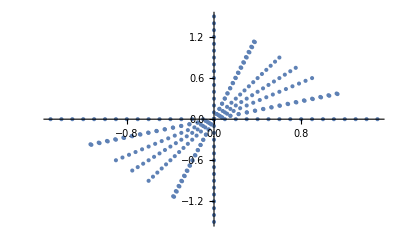

```mathematica
(* Creating list of initial Values *)
rangev0=Range[-1.5,1.5,0.1];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
ListPlot[listv0]
```

```mathematica
(* Initial Values *)
testRow=20;
linemax=45;

steps=1;

e=0.0001;
lvlmin=1;
lvlmax=3;

ic=ib;
{ia, ic}
```

{-Graphics-,-Graphics-}

```mathematica
(*See*)
pyrfiac=pyrfi[ia,ic,testRow,lvlmax];
Plot[{pyrfiac[[1,1,1]][x],pyrfiac[[1,2,1]][x]},{x,1,103}];
Plot[{pyrfiac[[lvlmax,1,1]][x],pyrfiac[[lvlmax,2,1]][x]},{x,1,103}];
Plot[{pyrfiac[[lvlmax,1,2]][x],pyrfiac[[lvlmax,2,2]][x],-e,+e},{x,1,103}];
```

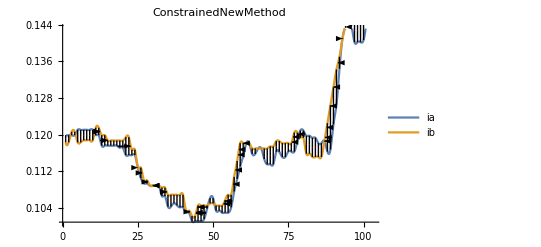

```mathematica
seeAllLine[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]
```

#### Little Test: Full image

```mathematica
(* Stereo Depth result *)
steps=1;

e=0.0001;
lvlmin=1;
lvlmax=3;

depth=stereoDepth[listv0,ia,ic,lvlmax,{lvlmin,lvlmax},Range[1,103,steps],Range[1,linemax],e,"ConstrainedNewMethod"];
Dimensions[depth]
```

{45,103,5}

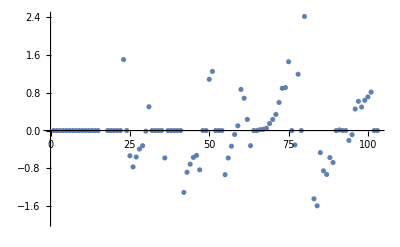

```mathematica
ListPlot[depth[[testRow,All,1]]]
```

```mathematica
(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
,{r,linemax}];

Dimensions[resTable]
```

{45}

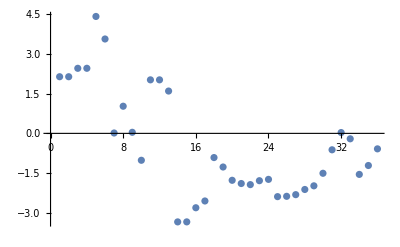

```mathematica
ListPlot[resTable[[testRow,All,1]]]
```

```mathematica
(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,-resTable[[r,All,1]]}]
,{r,linemax}];

Dimensions[realPVTable]
realPVTable;
```

{45}

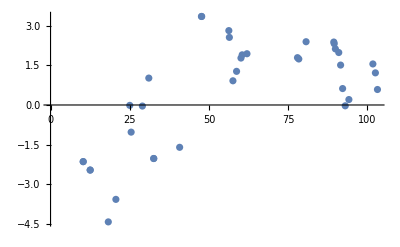

```mathematica
ListPlot[realPVTable[[testRow,All]]]
```

```mathematica
(* We combine solutions for each coordinate *)
resPVTable=Table[
combinePV[realPVTable[[r]]]

,{r,linemax}];
Dimensions[resPVTable]
```

Part::partw: Part 61 of {{18,3.45445},{18,3.54771},{22,-1.49996},{25,0.533193},{26,0.76833},{27,0.558939},{28,0.390287},{29,0.320098},{30,-0.503048},{30,0.0128995},«50»} does not exist.

Part::partw: Part 65 of {{16,2.42555},{18,-1.75391},{18,-1.75377},{18,3.54672},{18,3.54773},{19,-2.14078},{21,-1.70903},{22,-1.93749},{25,0.499785},{26,1.20124},«54»} does not exist.

Part::partw: Part 70 of {{10,-1.93708},{10,-1.93695},{14,1.68621},{14,1.68724},{15,-0.526161},{15,0.0306166},{17,-2.48156},{20,-0.0169411},{22,0.},{27,1.11596},«59»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{45}

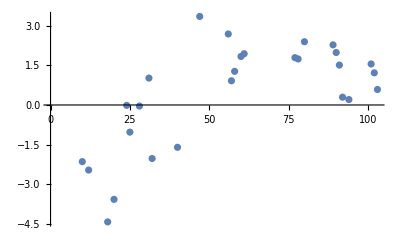

```mathematica
ListPlot[resPVTable[[testRow,All]]]
```

```mathematica
createReplaceValues[resPVTable_]:=Block[{rows},(
rows=Length[resPVTable];
Flatten[Table[
Thread[Thread[{resPVTable[[r,All,1]],r}-0.5]->resPVTable[[r,All,2]]]
,{r,rows}],1]
)]
```

```mathematica
values=createReplaceValues[resPVTable];
Dimensions[values]
```

{1687}

```mathematica
values[[103*3]]
```

{41.5,5.5}→1.47091

```mathematica
im=Image[Table[0,{y,linemax},{x,103}]]
```

-Graphics-

```mathematica
imm=ReplaceImageValue[im, values[[1;;103*15]]]

min
max
imm=ImageAdjust[imm,{min,max}]

Min[ImageData[imm]]
Max[ImageData[imm]]
```

-Graphics-

0.

0.691094

-Graphics-

0.

1.

```mathematica
ImageReflect[imm]
```

-Graphics-

```mathematica
GraphicsRow[{ImageReflect[imm],ImageAdjust[id]}]
```

-Graphics-